# The Central Limit Theorem

Why are we so concerned with means? Two reasons are: they give us a middle ground for comparison, and they are easy to calculate. In this lesson, we will study means and the central limit theorem. CLT is a powerful statistical theory states that given a sufficiently large sample size from any population, the mean of all samples from the same population tends toward a normal distribution.

## The Sampling Distribution

A sampling distribution is a probability distribution of a statistic obtained through a large number of samples drawn from a specific population. Let’s “discover” the Central Limit Theorem empirically, by looking at the lottery game. The lottery rule is: pick 5 numbers out of 69. You also choose 1 Power Ball number out of 26. See if your numbers match the numbers selected at the next drawing.

To make is simpler, we just pick 6 integers from 1 to 69:

```mathematica
RandomInteger[{1,69},6]
```

{17,11,9,57,11,43}

These random integers are uniformly distributed, so if we make a histogram of them, it’ll be flat.

Make a histogram of 1000 random pick of numbers from 1 to 69. We can see that the lottery numbers are uniformly distributed from 1 to 69.

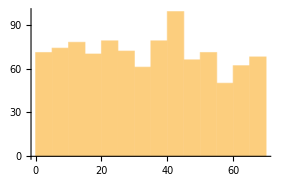

```mathematica
Histogram[RandomInteger[{1,69},1000]]
```

With 100,000 numbers the histogram is almost exactly flat:

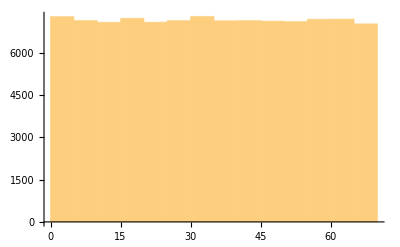

```mathematica
Histogram[RandomInteger[{0,69},100000]]
```

Now let’s start finding the mean of each ticket (sample). Repeat it many times.

This finds the mean of 6 random integers:

```mathematica
Mean[RandomInteger[{1,69},6]]//N
```

36.

Here is a list of 10 such means:

```mathematica
Table[Mean[RandomInteger[{1,69},6]],10]//N
```

{23.6667,42.5,35.3333,40.3333,35.,30.6667,42.5,28.1667,23.,49.8333}

Here is the distribution of 1000 such means:

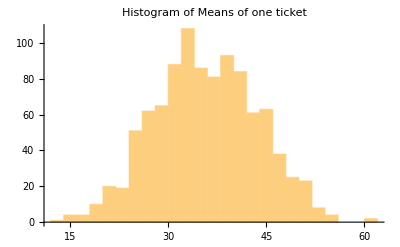

```mathematica
Histogram[Table[Mean[RandomInteger[{1,69},6]],1000],PlotLabel->"Histogram of Means of one ticket"]
```

Here is the distribution for 100,000 means:

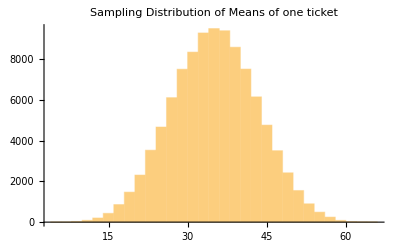

```mathematica
Histogram[Table[Mean[RandomInteger[{1,69},6]],100000],PlotLabel->"Sampling Distribution of Means of one ticket"]
```

The distribution for the means is not flat; instead it’s a bell-shaped curve.

It’s easier to see the shape of the curve if we use smaller bins; here width 0.5:

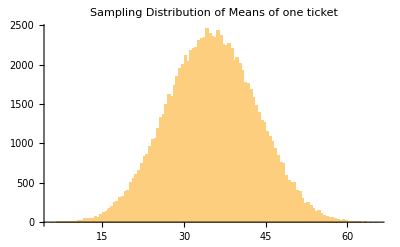

```mathematica
Histogram[Table[Mean[RandomInteger[{1,69},6]],100000],{0.5},PlotLabel->"Sampling Distribution of Means of one ticket"]
```

If we use a larger sample size to calculate the mean, we still get a very similar result except the distribution is narrower:

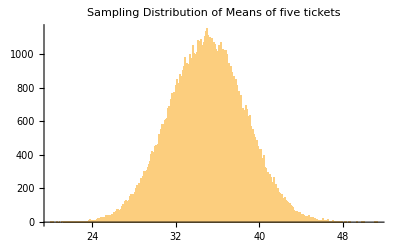

```mathematica
Histogram[Table[Mean[RandomInteger[{1,69},30]],100000],{.1},PlotLabel->"Sampling Distribution of Means of five tickets"]
```

The crucial thing about the Central Limit Theorem is that it holds for a wide range of different underlying random distributions.

This distribution of the number of texts students received during class is right-skewed:

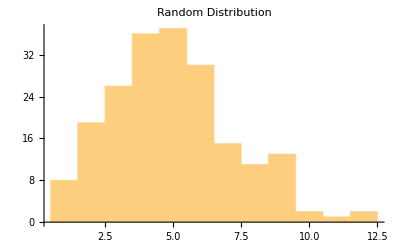

```mathematica
Histogram[RandomVariate[PoissonDistribution[5],200],PlotLabel->"Random Distribution"]
```

The distribution of the means is still a bell shape:

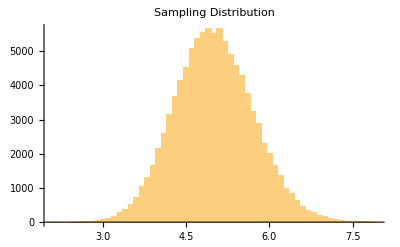

```mathematica
Histogram[Table[Mean[RandomVariate[PoissonDistribution[5],10]],100000],{0.1},PlotLabel->"Sampling Distribution"]
```

## The Normal Distribution

Let’s compare the results from data with an actual normal distribution.

Here is data from 100,000 lottery tickets:

```mathematica
data=Table[Mean[Table[RandomInteger[{1,69}],6]],100000];
```

The mean of this data is very close to (b+a)/2:

```mathematica
mean=Mean[data]//N
```

34.9955

This is the standard deviation of the data should be about (b-a)/(√(12n)):

```mathematica
std=StandardDeviation[data]//N
```

8.13392

Make a plot of a normal distribution with this mean and standard deviation:

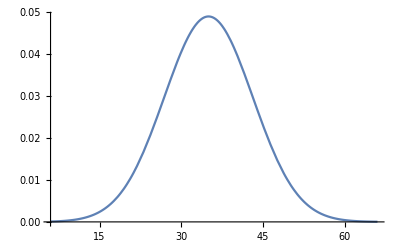

```mathematica
plot=Plot[PDF[NormalDistribution[mean,std],x],{x,6,66}]
```

To compare with histograms, we want the histogram (like the distribution) to be normalized to have total area 1.

Normalize the histogram so its total area is 1:

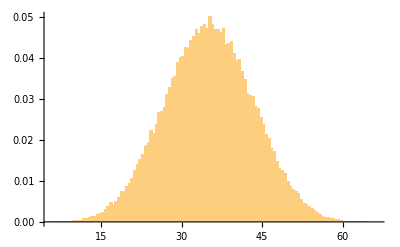

```mathematica
hist=Histogram[data,{.5},"PDF"]
```

Show the histogram and plot together; they agree!

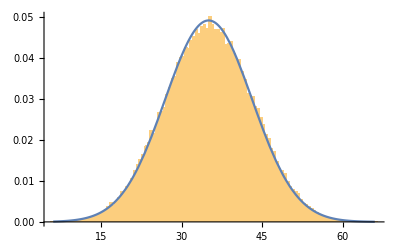

```mathematica
Show[hist,plot]
```

## Towards the Normal Distribution

If we don’t average multiple numbers at all, we’ll just see the underlying distribution of those numbers.  Let’s see what happens if we average successively more numbers.

Here’s the result “average 1 number” (i.e not averaging at all):

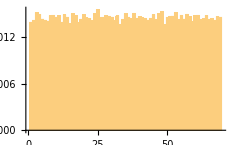

```mathematica
Histogram[Table[Mean[Table[RandomInteger[{1,69}],1]],100000],{1},"PDF"]
```

Here’s the result averaging 2 numbers:

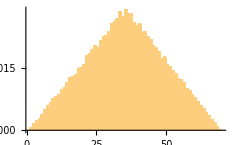

```mathematica
Histogram[Table[Mean[Table[RandomInteger[{1,69}],2]],100000],{1},"PDF"]
```

Here are the results averaging up to 10 numbers:

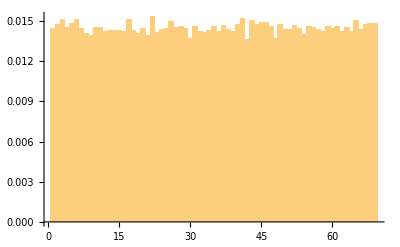
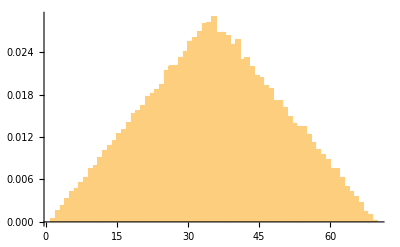
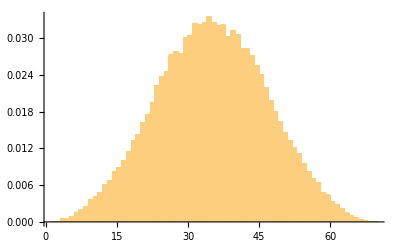
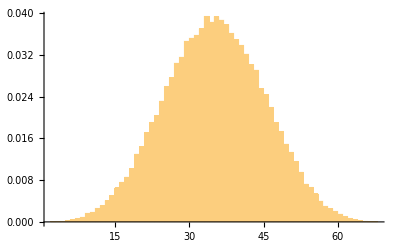
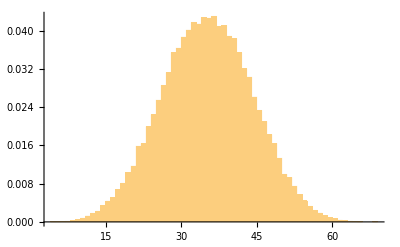
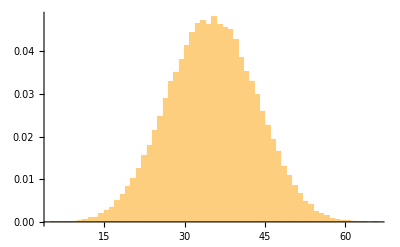
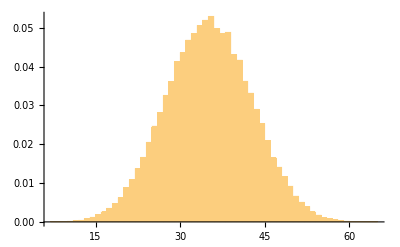
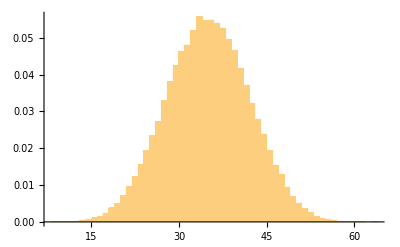

```mathematica
Table[Histogram[Table[Mean[Table[RandomInteger[{1,69}],n]],100000],{1},"PDF"],{n,10}]
```

Beyond about 5 numbers, the results are indistinguishable: the distribution has converged to the normal distribution, just as the Central Limit Theorem says it should.

## Exercise

What is the distribution of the average weekly stock price for GE?

Plot the stock price for GE since ten years ago:

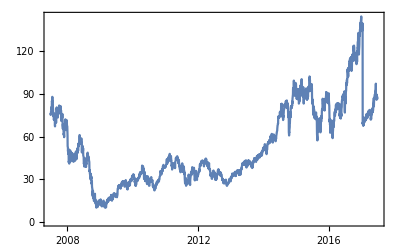

```mathematica
DateListPlot[FinancialData["USD",{Now-LinguisticAssistant,Now}]]
```

Further Explorations

Investigate the standard deviation of the sampling distribution.

Investigate the distribution of the average daycare tuition in Boston or other distribution that you are interested in.

Authorship information

Jie Frye

June 27, 2017

jiefrye@gmail.com

References

Introductory Statistics by OpenStaX.